Copyright (c) 2021 Jason Pereira jason.pereira@york.ac.uk

Permission is hereby granted, free of charge, to any person obtaining a copy
of this software and associated documentation files (the “Software”), to deal
in the Software without restriction, including without limitation the rights
to use, copy, modify, merge, publish, distribute, sublicense, and/or sell
copies of the Software, and to permit persons to whom the Software is
furnished to do so, subject to the following conditions:

The above copyright notice and this permission notice shall be included in all
copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED “AS IS”, WITHOUT WARRANTY OF ANY KIND, EXPRESS OR
IMPLIED, INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,
FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL THE
AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM, DAMAGES OR OTHER
LIABILITY, WHETHER IN AN ACTION OF CONTRACT, TORT OR OTHERWISE, ARISING FROM,
OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE
SOFTWARE.

```mathematica
ScalingMin[f_,Fcon_]:=Fcon
ScalingMax[f_,Fcon_]:=(1-(√(1-f)+√(1-Fcon))^2)/f

(*Scaling for the three channels*)

(*Constant*)
ScalingPauli[f_,Fcon_]:=Fcon
(*Constant below a certain value of f*)
ScalingClassical[f_,Fcon_]:=(Piecewise[{{1/2 √(-(-2+Cos[2 Δθ]+Cos[6 Δθ]-4 f Cos[4 Δθ] (f Cos[2 Δθ]-√(1-f^2) Sin[2 Δθ]))/f^2), f≥(√2 Abs[Sin[Δθ]] (2+2 Cos[2 Δθ]+Cos[4 Δθ]))/(√(2+Cos[2 Δθ]-Cos[6 Δθ]))}, {Abs[Cos[Δθ]+Cos[3 Δθ]]/(√(2+2 Cos[2 Δθ]+Cos[4 Δθ])), True}}])/.Δθ->1/2 ArcCos[(6^(1/3)+(-9+18 Fcon^2+√(75+324 Fcon^2 (-1+Fcon^2)))^(2/3))/(6^(2/3) (-9+18 Fcon^2+√(75+324 Fcon^2 (-1+Fcon^2)))^(1/3))]
(*0 below a certain value of f*)
ScalingUnitary[f_,Fcon_]:=Piecewise[{{Cos[ArcCos[f]+ArcCos[Fcon]]/f, f>Cos[1/2 (π-2 ArcCos[Fcon])]}, {0, True}}]
```

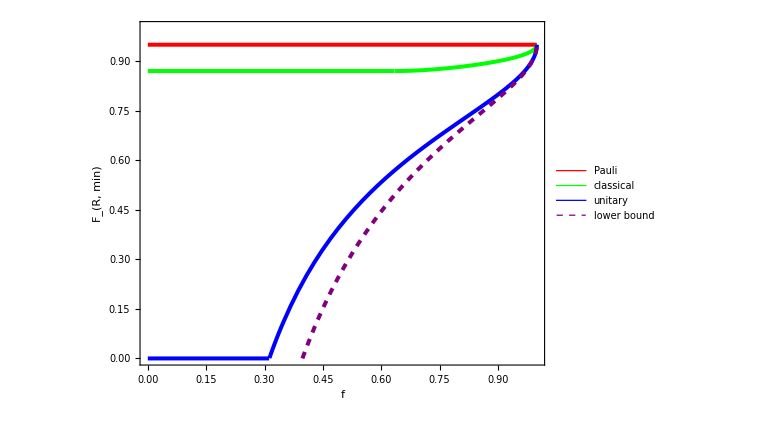

```mathematica
FconVal=0.95;
Plot[{ScalingPauli[f,FconVal],ScalingClassical[f,FconVal],ScalingUnitary[f,FconVal],ScalingMax[f,FconVal]},{f,0,1},PlotRange->{{0,1},{0,1}},ImageSize->Large,PlotStyle->{Directive[Red,Thickness[0.005]],Directive[Green,Thickness[0.005]],Directive[Blue,Thickness[0.005]],Directive[Purple,Thickness[0.005],Dashed]},FrameStyle->Directive[20,Thick,Bold],FrameLabel->{"f","F_(R, min)"},TicksStyle->Thick,Frame->{{True,False},{True,False}},AspectRatio->3/4,PlotLegends->Placed[{"Pauli","classical","unitary","lower bound"},{0.8,0.22}],BaseStyle->16]
```